A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)

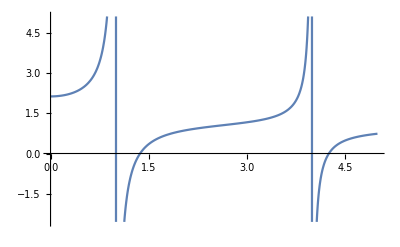

```mathematica
polzMdl=A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)
Plot[polzMdl/.{A1->1,f1->1,f2->2,E1->1,E2->4,h->1},{ω,0,5}]
```

## 2 component model

```mathematica
Real[polzMdl/.{A1->1,f1->1,f2->2,E1->1,E2->4,ω->1.5,h->1}]
```

Real[0.345455]

```mathematica
ToFreqTwoLevel=Solve[0==polzMdl/.{A1->0},ω]
ToFreqTwoLevel=ω/.ToFreqTwoLevel[[2]]
FullSimplify[ToFreqTwoLevel,Assumptions->{h>0}]
```

{{ω→-(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))},{ω→(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))}}

(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))

(√(E2^2 f1+E1^2 f2))/(√(f1+f2) h)

```mathematica
ToFreqTwoLevel=Simplify[ToFreqTwoLevel/.f2->X1 f1]
```

(√(f1 (E2^2+E1^2 √X1)))/(√(f1 h^2 (1+√X1)))

```mathematica
RatioVal=Solve[ωto==ToFreqTwoLevel,X1]
RatioVal=FullSimplify[RatioVal, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals, ωto∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0, ωto>0}]
```

{{X1→((E2^2-h^2 ωto^2)^2)/((-E1^2+h^2 ωto^2)^2)}}

{{X1→((E2^2-h^2 ωto^2)^2)/((E1^2-h^2 ωto^2)^2)}}

```mathematica
DerivTOWithX=D[ToFreqTwoLevel,X1]
DerivTOWithX=FullSimplify[DerivTOWithX, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(E1^2 f1)/(4 √(f1 h^2 (1+√X1)) √(f1 (E2^2+E1^2 √X1)) √X1)-(f1 h^2 √(f1 (E2^2+E1^2 √X1)))/(4 (f1 h^2 (1+√X1))^(3/2) √X1)

((E1-E2) (E1+E2))/(4 h (1+√X1)^(3/2) √(E2^2+E1^2 √X1) √X1)

```mathematica
FracUncX=(1/DerivTOWithX)δωTo/X1/.RatioVal[[1]]
Simplify[FracUncX, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals, ωto∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0, ωto>0}]
```

(4 h δωTo (1+√(((E2^2-h^2 ωto^2)^2)/((E1^2-h^2 ωto^2)^2)))^(3/2) √(E2^2+E1^2 √(((E2^2-h^2 ωto^2)^2)/((E1^2-h^2 ωto^2)^2))))/((E1-E2) (E1+E2) √(((E2^2-h^2 ωto^2)^2)/((E1^2-h^2 ωto^2)^2)))

(4 h δωTo (Abs[E1^2-h^2 ωto^2]+Abs[E2^2-h^2 ωto^2])^(3/2) √(E2^2 Abs[E1^2-h^2 ωto^2]+E1^2 Abs[E2^2-h^2 ωto^2]))/((E1-E2) (E1+E2) Abs[E1^2-h^2 ωto^2] Abs[E2^2-h^2 ωto^2])

## 3 component system

Now lets try this again but with the offset

```mathematica
ToFreqTwoLevel=Solve[0==polzMdl,ω]
```

{{ω→-1/(√2)(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-1/(A1 h^4)(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))))},{ω→1/(√2)(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-1/(A1 h^4)(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))))},{ω→-1/(√2)(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)+1/(A1 h^4)(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))))},{ω→1/(√2)(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)+1/(A1 h^4)(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))))}}

Which of these roots do i want?? 
ok looks like the second

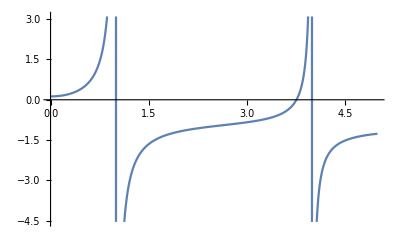

{{ω→-3.76051},{ω→3.76051},{ω→0.-0.37607 ⅈ},{ω→0.+0.37607 ⅈ}}

```mathematica
Plot[polzMdl/.{A1->-1,f1->1,f2->2,E1->1,E2->4,h->1},{ω,0,5}]
N[ToFreqTwoLevel/.{A1->-1,f1->1,f2->2,E1->1,E2->4,h->1}]
```

```mathematica
ToFreqThreeComp=ω/.ToFreqTwoLevel[[2]]
ToFreqThreeComp=ToFreqThreeComp/.{f2->X1 f1,A1->X2 f1}
```

(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)

(√(E1^2/h^2+E2^2/h^2+1/(h^2 X2)+X1/(h^2 X2)-(√(h^4 (f1^2+2 f1^2 X1+f1^2 X1^2+2 E1^2 f1^2 X2-2 E2^2 f1^2 X2-2 E1^2 f1^2 X1 X2+2 E2^2 f1^2 X1 X2+E1^4 f1^2 X2^2-2 E1^2 E2^2 f1^2 X2^2+E2^4 f1^2 X2^2)))/(f1 h^4 X2)))/(√2)

```mathematica
Solve[ωto==ToFreqThreeComp,X1]
```

{{X1→-((E2^2-h^2 ωto^2) (-1-E1^2 X2+h^2 X2 ωto^2))/(-E1^2+h^2 ωto^2)}}

```mathematica
ToFreqThreeComp=FullSimplify[ToFreqThreeComp, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(√((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/(h^2 X2)))/(√2)

```mathematica
DerivTOWithX=FullSimplify[D[ToFreqThreeComp,X1], Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(1-(1+X1-E1^2 X2+E2^2 X2)/(√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2)))/(2 √2 h X2 √((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/X2))